```mathematica
<<myFunctionsMathematica8.m
```

SetDelayed::write: Tag Real in (-« 386 »)[z_] is Protected.

{Temporary}

```mathematica
bestzero[n_]:=1/2+I*t[n]
```

```mathematica
bestzero[1]
```

1/2+14.13472514173469379045725198356247027078425711569924317568556746014996342980925676494901039317156101277920297154879743676614269146988225458250536323944713778041338123720597054962195586586020055556672583601077370020541098266150754278051744259130625448197865107230493872562973832157742039521572567480933214003499046803434626731442092037738548714137831735639699536542811307968053149168852906782082298049264338666734623320078758761792005604868054356801444424651065597568665903228686510544859444320624072727032094274522213048748720924123851418351460542790152447833835425453344004487936806761697300819000731393854983736215013045167269683892003917628512321285422052396913342583227533516406016976352756375896953767492033612720925999173042707568308795118445348918008630082648312516911271068291052375961797743181517071354531677549515382893784903647470972701994848553220925357435790922612524773659551801697523346121397731600535412592674745572587780147260983080897860071253208750939599796666067537838121489190886497727755442065653205241 ⅈ

## n \mapsto t[n] is defined as a table in myFunctionsPureCodeV8 copy.nb, whhich is loaded by myFunctionsMathematica8.m. The table was created in my2ndEditOdlyzkoAccrtZrs6dec15.nb. It is from a table on Odlyzko’s site.

```mathematica
poincareNorm[q_]:=Log[(1+Abs[q])/(1-Abs[q])]
```

```mathematica
poincareNorm[1+I]
```

ⅈ π+Log[-(1+√2)/(1-√2)]

```mathematica
zetaIterate[s_,iteratenumber_]:=Module[{kk,w},
w=s;
For[kk=0,kk<iteratenumber,kk++;w=Zeta[w];
If[Abs[w]>10^10,Break[]]];
Return[w]
];
Attributes[zetaIterate]=Listable
```

Listable

N   1

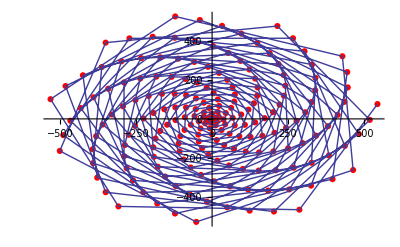

Null

N   2

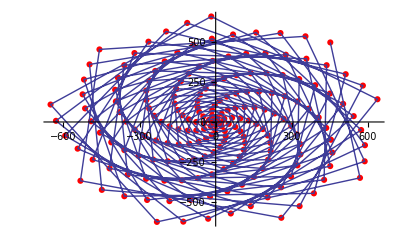

Null

N   3

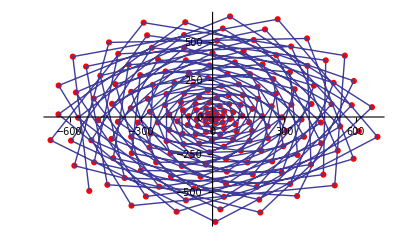

Null

N   4

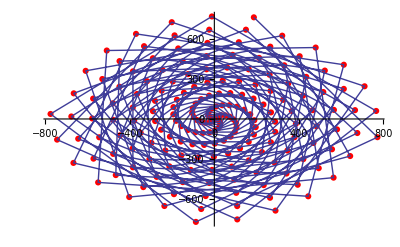

Null

N   5

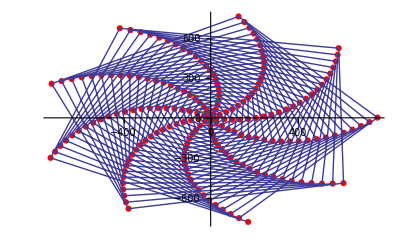

Null

N   6

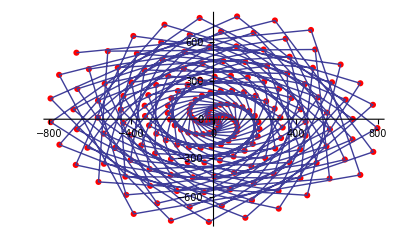

Null

N   7

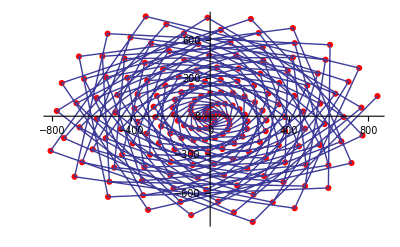

Null

N   8

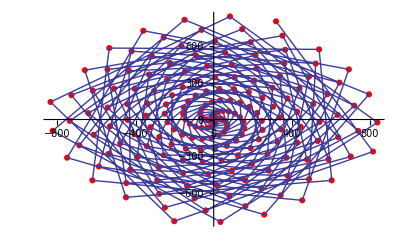

Null

N   9

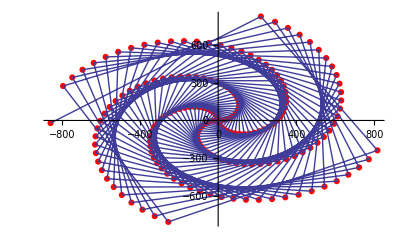

Null

N   10

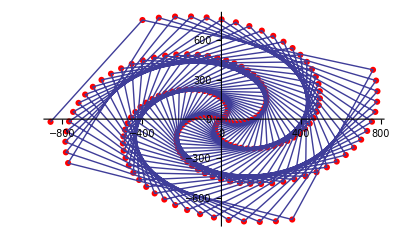

Null

psiNrhoNspirals3apr17no6

```mathematica
stream=OpenRead["zeta1fixedpts13dec15"];
ls=ReadList[stream];
Close[stream];
streem=OpenWrite["psiNrhoNspirals3apr17no6"];
precision=400;
depth=200;
For[n=0,n<10,n++;
data={};

fxx=ls[[n,2]];

k=1;
zr=bestzero[n];
zeros={zr};

arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point];




Write[streem,{n,k,zr}];

For[k=1,k<depth,k++;
startcenter=fxx;
x=Last[zeros];
zr=FindRoot[zetaIterate[s,1]-x,{s,startcenter},PrecisionGoal->precision,WorkingPrecision->precision][[1,2]];
zeros=Append[zeros,zr];

arg=Arg[zr-fxx];
la=Log[Abs[zr-fxx]];
point={la*Cos[arg],la*Sin[arg]};
data=Append[data,point];




Write[streem,{n,k,zr}]
]; (* close k loop *)
p=ListPlot[data,PlotStyle->{Red,PointSize[.011]}];
pjoined=ListPlot[data,Joined->True];

Print["N   ",n];
Print[Print[Show[p,pjoined]]]
]; (* close n loop *)
Close[streem]
```